```mathematica
F[x_,y_]:={6x^5 Sin[y]-Sin[x]y^5,x^6 Cos[y]+5Cos[x] y^4}
```

```mathematica
L[t_]:=Normalize[{-1,-1}]t+{Pi/2,0}
```

```mathematica
Integrate[Dot[F@@L[t],L'[t]],{t,0,π/(√2)}]
```

-π^5/32

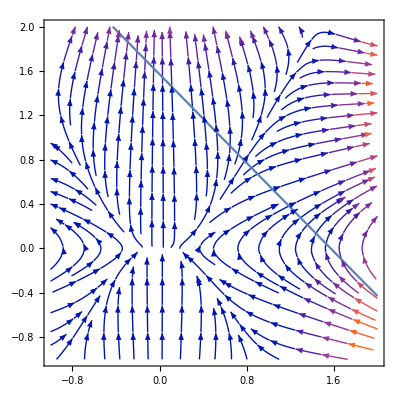

```mathematica
Show[
StreamPlot[F[x,y],{x,-1,2},{y,-1,2}],
ContourPlot[x+y==Pi/2,{x,-1,2},{y,-1,2}]]
```

```mathematica
F[u_,v_]:={u+v^2,u,v}
```

```mathematica
Integrate[Integrate[Norm[Cross[D[F[u,v],u],D[F[u,v],v]]],{u,0,4}],{v,0,1}]
Integrate[Norm[Cross[D[F[u,v],u],D[F[u,v],v]]],{u,0,4},{v,0,1}]
```

2 (√6+ArcTanh[√(2/3)])

2 √6+Log[5+2 √6]

```mathematica
2 (√6+ArcTanh[√(2/3)])==2 √6+Log[5+2 √6]//FullSimplify
```

```mathematica
F[x_,y_]:={x,y,√(R^2-x^2-y^2)}
```

```mathematica
2Integrate[Norm[Cross[D[F[u,v],u],D[F[u,v],v]]],{u,v}∈ImplicitRegion[(x-R/2)^2+y^2<=R^2/4,{x,y}],Assumptions->R∈PositiveReals]
```

2 (-2+π) R^2

```mathematica
$Assumptions=x∈Reals&&y∈Reals&&z∈Reals&&(Dt[x]|Dt[y]|Dt[z])∈Vectors[{3},Reals];
```

```mathematica
Simplify@TensorReduce[TensorWedge[16Dt[x]+6Dt[y]-4Dt[z],5Dt[x]+15Dt[y]+2Dt[z]]]
```

210 Dt[x]\[TensorWedge]Dt[y]+52 Dt[x]\[TensorWedge]Dt[z]+72 Dt[y]\[TensorWedge]Dt[z]

```mathematica
res=Integrate[1,{x,y,z}∈ImplicitRegion[
Abs[x]<=b&&Abs[y]<=b&&x^2+y^2+z^2<=a^2,{x,y,z}
],Assumptions->a∈PositiveReals&&b∈PositiveReals&&a>2b]
```

2/3 (4 b^2 √(a^2-2 b^2)-4 b (-3 a^2+b^2) ArcTan[b/(√(a^2-2 b^2))]-2 ⅈ a^3 (Log[(a+b) (ⅈ a^2-ⅈ a b+b (-ⅈ b+√(a^2-2 b^2)))]-Log[(a-b) (ⅈ a^2+ⅈ a b+b (-ⅈ b+√(a^2-2 b^2)))]))

```mathematica
2Integrate[√(a^2-x^2-y^2),{x,-b,b},{y,-b,b},Assumptions->a∈PositiveReals&&b∈PositiveReals&&a>√2 b]
```

2/3 (-4 a^3 ArcCot[(a √(a^2-2 b^2))/b^2]+4 b (b √(a^2-2 b^2)+(3 a^2-b^2) ArcTan[b/(√(a^2-2 b^2))]))

```mathematica
%//FullSimplify
```

2/3 (-4 a^3 ArcCot[(a √(a^2-2 b^2))/b^2]+4 b (b √(a^2-2 b^2)+(3 a^2-b^2) ArcTan[b/(√(a^2-2 b^2))]))